## Formulas for Rocket and Non-working code (Not Used for Program Execution)

Acceleration due to gravity at Earth’s Surface in m/s^2

```mathematica
g0=9.8;
```

Specific Impuse of the engine in s. Vg is the velocity of the exhaust gas of the engine

```mathematica
Isp[Vg_]=Vg/g0;
```

Delta V of the engine in m/s. mt is mass at current time (initial mass at time 0), Vg is exhaust gas of the engine, ρ0 is the atmospheric pressure at altitude, R is the radius of the planet, h is the current altitude, H is the scale height which is the increase in altitude for which the atmospheric pressure decreases by a factor of e, g0 is the acceleration due to gravity for Earth, DeltaT is the change in time, and v is the instantaneous velocity of the rocket.

```mathematica
Clear[DeltaV]
```

```mathematica
Vg=2500
```

2500

Vg of rockets today, can’t change much if you want to go into orbit, but we will make it manipulatable, and include launches that fail to make it into orbit.

```mathematica
R=6371000
```

6371000

Radius of Earth (m) for early calculations, will be made manipulatable.

```mathematica
ρ0=1.225
```

1.225

Air density at sea level at 15° C, will be made manipulatable.

```mathematica
H=7000
```

7000

Scale Height does vary with temperature, but at this point in our project, the various is negligible, and will be found later.

```mathematica
α=4000
```

4000

α is the mass of gas the engine expels per second. (kg/s)

```mathematica
mt[m0_,T_]:=m0-α*T
```

```mathematica
m0=2970000
```

2970000

```mathematica
mt[T_]:=m0-α T
```

T is time elapsed so far.
m0 is the initial mass of the rocket + fuel. This will be calculated when the size of the rocket can be manipulated. (for now, we use the mass of Saturn V)

```mathematica
(*DeltaV[DeltaT_]:=(Vg*α-mt[DeltaT-1]*g0*(R/(R+h[DeltaT-1]))^2-ρ0^((-h[DeltaT-1])/H)*v[DeltaT-1]^2)/mt[DeltaT-1]*DeltaT;*)
```

```mathematica
DeltaV[0]=0;
DeltaV[1]=(Vg α-mt[1]g0(R/(R+h))^2)/mt[1];
DeltaV[DeltaT_]:=(Vg α-mt[DeltaT]g0 (R/(R+h))^2-ρ0^((-h[DeltaT])/H)v[DeltaT-1]^2)/mt[DeltaT] DeltaT
```

```mathematica
v[0]=0;
v[1]= DeltaV[1];
v[DeltaT_]:=DeltaV[DeltaT-1]+DeltaV[DeltaT];
```

```mathematica
h[0]=0;
h[1]=v[1];
h[DeltaT_]:=h[DeltaT-1]+v[DeltaT]DeltaT;
```

```mathematica
mt[0]=m0;
mt[1]=m0-α;
mt[DeltaT_]:=mt[DeltaT-1]-α DeltaT;
```

Euller Method. Simplest and most crude method. If we see that the error presents itself as too great, we will refine it to Runga-Kutta 2, then see if that would be efficient enough.
When we have this figured out more, Vg, will be taken as a constant selected by the user, as well as ρ0, R, and H, to show various conditions of launch.

We’re in the process of finding exactly how to find v when v = v + DeltaV for at time T that has elapsed updating v T/DeltaT times for intervals of DeltaT.
When we do this, the h can also be updated each time for h = h + v*DeltaV.

```mathematica
DeltaV[2]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of 6371000 + h.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of DeltaV[2 - 1].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of 10000000 - 1.17981×10^21/(6371000 + h)^2.

General::stop: Further output of $RecursionLimit :: reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of MakeBoxes[6371000, StandardForm].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of MakeBoxes[h, StandardForm].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {Hold[MakeBoxes[6371000, StandardForm]], "+", Hold[MakeBoxes[h, StandardForm]]}.

General::stop: Further output of $RecursionLimit :: reclim2 will be suppressed during this calculation.

10000000-(1.17663×10^21)/(6371000+h)^2+1.225^((10000000-(1.17981×10^21)/(6371000+h)^2)/2966000+((10000000-(1.17981×10^21)/(1)^2)/2966000+(10000000-(1.17663×10^21)/(1)^2+1.225^((10000000-1)/2966000+(1+1)))))
 |  |  |  |

```mathematica
rocketDynamic[]=
DynamicModule[{Vg=2500,R=6371000,ρ0=1,α=4000,g0=-9.8,H=7000,h=0,v=0,Tcurrent=0.5,DeltaV=0,mt=2750000,TotalDV=0,values={},time=0,mR=185000,m0=2750000,deltaT=0.5},
{For[Tcurrent,Tcurrent≤Dynamic[time],Tcurrent+=deltaT,
DeltaV=(Vg*α-mt*g0*(R/(R+h))^2-ρ0*ⅇ^(-h/H)*v^2)/mt*deltaT;
TotalDV=(Vg*α-mt*g0*(R/(R+h))^2-ρ0*ⅇ^(-h/H)*v^2)/mt*Tcurrent;
v+=DeltaV;
h+=v*deltaT;
mt=m0-α*Tcurrent;
If[mt≤mR,Break[]]
];
Graphics[{Blue,Text["Current Velocity: " <>ToString[v],{0,1}],Text["Current Altitude: " <>ToString[h],{0,0}],Text["Current DeltaV Total: "<>ToString[ TotalDV],{0,-1}]}],Slider[Dynamic[time],{1,500}]}
]
```

## Main Program

Currently only has the calculations program. Interface will be added in another program when calculations are complete.

Rocket Live new:

```mathematica
rocket[deltaT_,t_,r_,height_,dens_,fuel_]:=
Module[{Vg=2500,R=6371000,ρ0=1,area=r^2*Pi,α=12000,g0=9.8,H=7000,h=0,v=0,Tcurrent=deltaT,DeltaV=0,mt=r^2*height*dens+fuel,m0,TotalDV=0,values={},fuelcheck=True},
m0=mt;
For[Tcurrent,Tcurrent≤t,Tcurrent+=deltaT,
If[fuelcheck,
DeltaV=(Vg*α-mt*g0*(R/(R+h))^2-ρ0*area*ⅇ^(-h/H)*v^2)/mt*deltaT,
DeltaV=(-mt*g0*(R/(R+h))^2-ρ0*area*ⅇ^(-h/H)*v^2)/mt*deltaT];
If[mt≥m0-fuel,mt=m0-α*Tcurrent,fuelcheck=False];
v+=DeltaV;
h+=v*deltaT;
];
Framed[Graphics[{Blue,Text[Style["Current Velocity: " <>ToString[v]<>" m/s",Large],{0,.15}],Text[Style["Current Altitude: " <>ToString[h]<>" m",Large],{0,0}]}]]
]
```

```mathematica
Manipulate[rocket[.1,t,r,h,d,fm],
{t,0,500},
{r,3,10},
{h,50,200},
{d,10,50},
{fm,1500000,3500000}
]
```

```mathematica
rocketLive[deltaT_,t_,m0_,mR_,r_,ρ0_,g0_]:=
(* Values are that are inputted into the function:
"deltaT", (time interval upon which to calculate DeltaV, and thus other values, s)
"t", (total time to calculate through, s)
"m0", (initial gross mass of rocket, kg)
"mR", (dry mass of rocket, kg)
 *)
Module[{Vg=2500,R=6371000,α=34000,H=70000,h=0,v=0,Tcurrent=deltaT,DeltaV=0,mt=m0,values={},area=r^2*Pi},
(* Constants are introduced in the Module, as well as calculated values that vary through the launch. *)
(* The constants include:
"Vg" (velocity of gas leaving the rocket, m/s),
"R" (Radius of the Earth, m),
"ρ0" (pressure ar sea level, atm),
"α" (amount of gas leaving the rocket, kg/s),
"g0" (gravity, m/s^2),
"H" (scalar height--the increase in altitude for which the atmospheric pressure decreases by a factor of ⅇ, m)
 *)
(* The calculated values include:
"DeltaV", (change in velocity the rocket is capable of at an exact instance given the velocity, height, and the mass at the current time you are searching for the DeltaV, m/s)
"TotalDV", (change in velocity the rocket is capable of from time 0 to t, m/s)
"v", (velocity of rocket at given time, m/s)
"h", (height of rocket at given time, m)
"mt", (gross mass of rocket at given time, kg)
 *)
For[Tcurrent,Tcurrent≤t,Tcurrent+=deltaT,
DeltaV=(Vg*α-mt*g0*(R/(R+h))^2-ρ0*area*ⅇ^(-h/H)*v^2)/mt*deltaT;
v+=DeltaV;
(* "v" increases by DeltaV during each time interval *)
h+=v*deltaT;
(* "h" increases by the velocity(time interval) -> m/s(s) -> m *)
mt=m0-α*Tcurrent;
(* The current mass of the rocket will be the total gross mass with the amount of fuel consumed subtracting out *)
If[mt≤mR,Break[]];
(* More fuel can't be burned that is in the rocket *)
];
Framed[Graphics[{Blue,Text[Style["Current Velocity: " <>ToString[v]<>" m/s",Large],{0,.15}],Text[Style["Current Altitude: " <>ToString[h]<>" m",Large],{0,0}]}]]
]
```

```mathematica
Manipulate[rocketLive[.5,t,2750000,185000,5,1,9.8],{t,0,300}]
```

```mathematica
rocketGraph[deltaT_,t_,m0_,mR_,r_,ρ0_,g0_]:=
(* Values are that are inputted into the function:
"deltaT", (time interval upon which to calculate DeltaV, and thus other values, s)
"t", (total time to calculate through, s)
"m0", (initial gross mass of rocket, kg)
"mR", (dry mass of rocket, kg)
 *)
Module[{Vg=2500,R=6371000,α=34000,H=70000,h=0,v=0,Tcurrent=deltaT,DeltaV=0,mt=m0,values={},area=r^2*Pi},
(* Constants are introduced in the Module, as well as calculated values that vary through the launch. *)
(* The constants include:
"Vg" (velocity of gas leaving the rocket, m/s),
"R" (Radius of the Earth, m),
"ρ0" (pressure ar sea level, atm),
"α" (amount of gas leaving the rocket, kg/s),
"g0" (gravity, m/s^2),
"H" (scalar height--the increase in altitude for which the atmospheric pressure decreases by a factor of ⅇ, m)
 *)
(* The calculated values include:
"DeltaV", (change in velocity the rocket is capable of at an exact instance given the velocity, height, and the mass at the current time you are searching for the DeltaV, m/s)
"TotalDV", (change in velocity the rocket is capable of from time 0 to t, m/s)
"v", (velocity of rocket at given time, m/s)
"h", (height of rocket at given time, m)
"mt", (gross mass of rocket at given time, kg)
 *)
For[Tcurrent,Tcurrent≤t,Tcurrent+=deltaT,
DeltaV=(Vg*α-mt*g0*(R/(R+h))^2-ρ0*area*ⅇ^(-h/H)*v^2)/mt*deltaT;
v+=DeltaV;
(* "v" increases by DeltaV during each time interval *)
h+=v*deltaT;
(* "h" increases by the velocity(time interval) -> m/s(s) -> m *)
mt=m0-α*Tcurrent;
(* The current mass of the rocket will be the total gross mass with the amount of fuel consumed subtracting out *)
If[mt≤mR,Break[]];
(* More fuel can't be burned that is in the rocket *)
AppendTo[values,{v,h}]
];
Graphics[ListPlot[values,PlotRange->All,Frame->True,FrameLabel-> {"Velocity (m/s)","Altitude (m)"}]]
]
```

### Altitude vs. Velocity Plots

A plot that would be expected for a single stage rocket with atmospheric drag and gravity

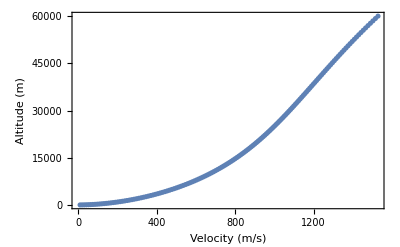

```mathematica
rocketGraph[.5,500,2750000,185000,5,1,9.8]
```

A plot for a single stage rocket without atmospheric drag or gravity

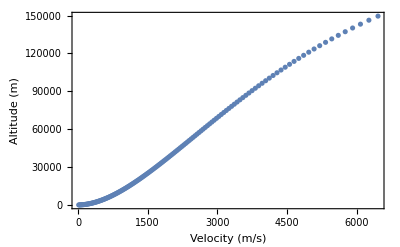

```mathematica
rocketGraph[.5,800,2750000,185000,5,0,0]
```

A plot for a singe stage rocket without atmospheric drag, but with gravity

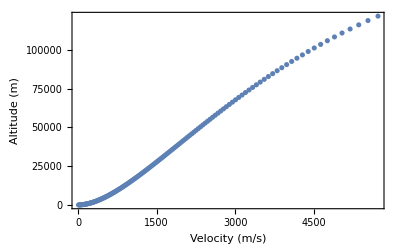

```mathematica
rocketGraph[.5,800,2750000,185000,5,0,9.8]
```

A plot for a single stage rocket with atmospheric drag, but no gravity. Note the lag in velocity as the rocket accelerates and that even though there is no gravity the rocket does not make it much higher than in the standard plot with drag and gravity.

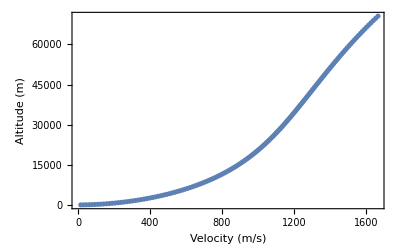

```mathematica
rocketGraph[.5,500,2750000,185000,5,1,0]
```

### Accuracy Testing

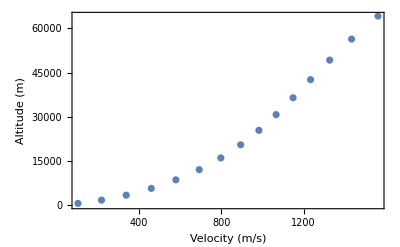

```mathematica
rocketGraph[5,500,2750000,185000,5,1,9.8]
```

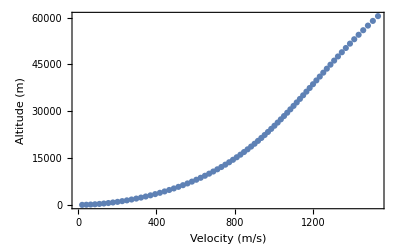

```mathematica
rocketGraph[1,500,2750000,185000,5,1,9.8]
```

```mathematica
rocketGraph[.5,500,2750000,185000,5,1,9.8]
```

-Graphics-

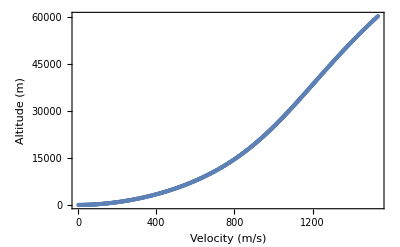

```mathematica
rocketGraph[.1,500,2750000,185000,5,1,9.8]
```

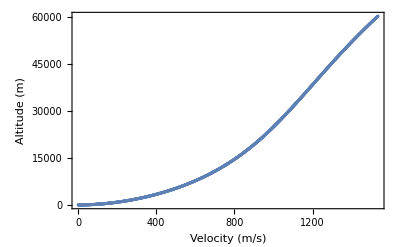

```mathematica
rocketGraph[.05,500,2750000,185000,5,1,9.8]
```

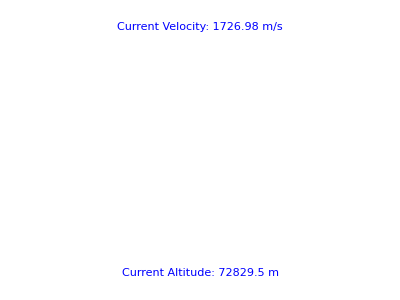

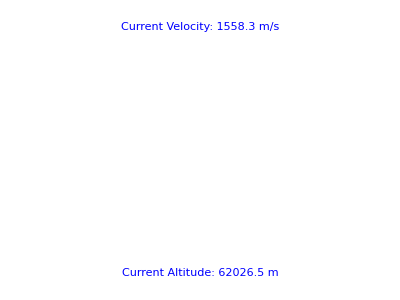

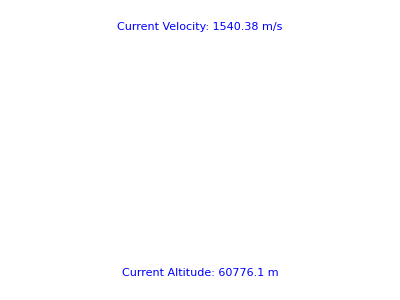

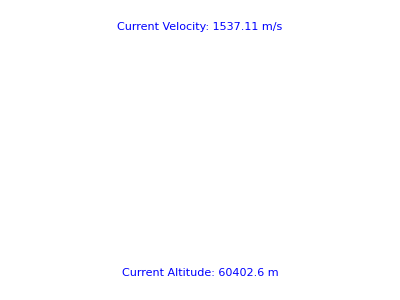

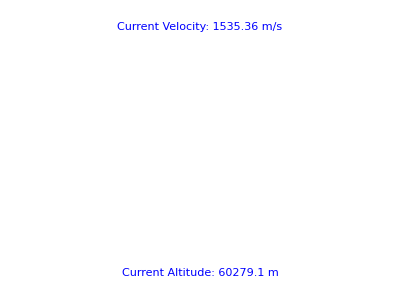

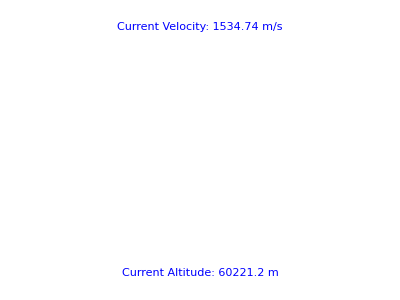

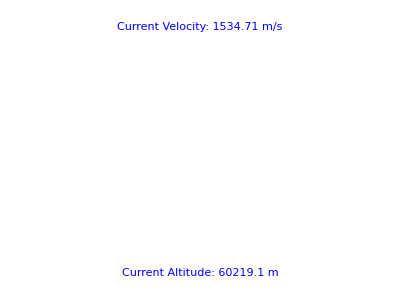

```mathematica
rocketLive[5,500,2750000,185000,5,1,9.8]
rocketLive[1,500,2750000,185000,5,1,9.8]
rocketLive[.5,500,2750000,185000,5,1,9.8]
rocketLive[.1,500,2750000,185000,5,1,9.8]
rocketLive[.05,500,2750000,185000,5,1,9.8]
rocketLive[.001,500,2750000,185000,5,1,9.8]
rocketLive[.0001,500,2750000,185000,5,1,9.8]
```

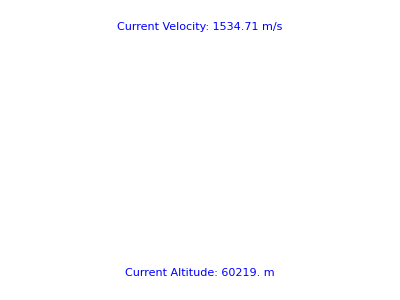

```mathematica
rocketLive[.00001,500,2750000,185000,5,1,9.8]
```